# Stirling permutation

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

In combinatorial mathematics, a Stirling permutation of order k is a permutation of the multiset 1, 1, 2, 2, …, k, k (with two copies of each value from 1 to k) with the additional property that, for each value i appearing in the permutation, the values between the two copies of i are larger than i. Wikipedia uses larger than i, whereas an example on the OEIS uses less than i. Both work. For instance, the 15 Stirling permutations of order three are

```mathematica
StirlingPermutations[3]
```

{{3,3,2,2,1,1},{2,3,3,2,1,1},{2,2,3,3,1,1},{2,2,1,3,3,1},{2,2,1,1,3,3},{3,3,1,2,2,1},{1,3,3,2,2,1},{1,2,3,3,2,1},{1,2,2,3,3,1},{1,2,2,1,3,3},{3,3,1,1,2,2},{1,3,3,1,2,2},{1,1,3,3,2,2},{1,1,2,3,3,2},{1,1,2,2,3,3}}

```mathematica
FromDigits/@StirlingPermutations[3]
```

{332211,233211,223311,221331,221133,331221,133221,123321,122331,122133,331122,133122,113322,112332,112233}

```mathematica
Row/@StirlingPermutations[3]
```

{332211,233211,223311,221331,221133,331221,133221,123321,122331,122133,331122,133122,113322,112332,112233}

The number of Stirling permutations of order k is given by the double factorial (2k-1)!!. Stirling permutations were introduced by Gessel and Stanley in 1978 to show that certain numbers (the numbers of Stirling permutations with a fixed number of descents) are non-negative. They chose this name because of a connection to certain polynomials defined from the Stirling numbers, which are in turn named after 18th-century Scottish mathematician James Stirling.

Stirling permutations may be used to describe the sequences by which it is possible to construct a rooted plane tree with k edges by adding leaves one by one to the tree. For, if the edges were numbered by the order in which they were inserted, then the sequence of numbers in an Euler tour of the tree (formed by doubling the edges of the tree and traversing the children of each node in a left to ride order) is a Stirling permutation. Conversely, every Stirling permutation describes a tree construction sequence, in which the next edge closer to the root from an edge labeled i is the one whose pair of values most closely surrounds the pair of i values in the permutation.

Stirling permutations have been generalized to the permutations of a multiset with more than two copies of each value. Researchers have also studied the number of Stirling permutations that avoid certain patterns.

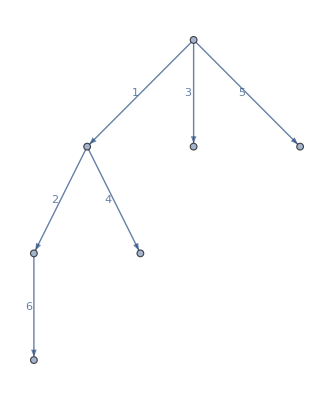

```mathematica
StirlingPermutationGraph[{1,2,6,6,2,4,4,1,3,3,5,5}]
```

```mathematica
GraphTree[StirlingPermutationGraph[{1,2,6,6,2,4,4,1,3,3,5,5}]]
```

-Graphics-

All trees of order 3:

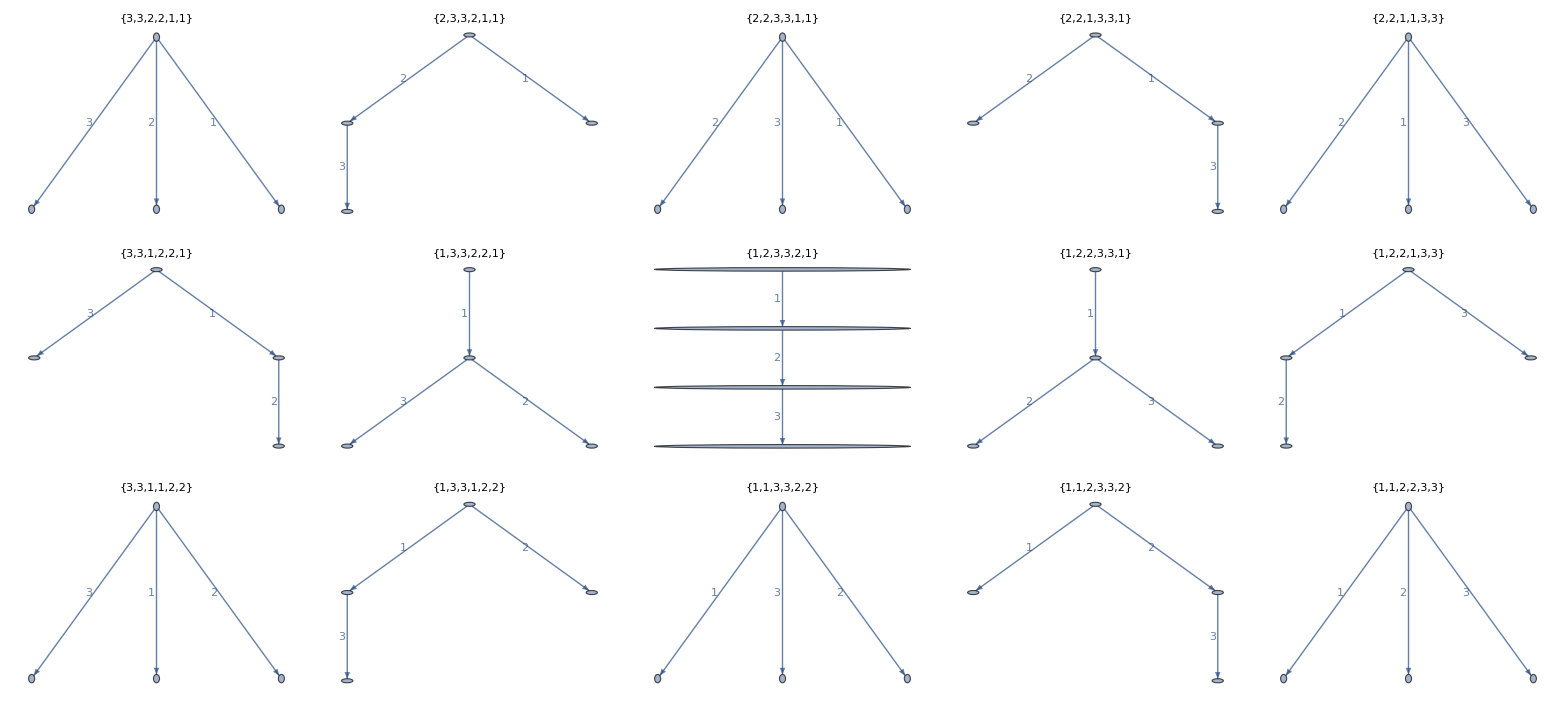

```mathematica
Grid[Partition[StirlingPermutationGraph[#,PlotLabel->#]&/@StirlingPermutations[3],5],Dividers->All]
```

All trees of order 4:

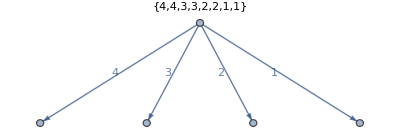
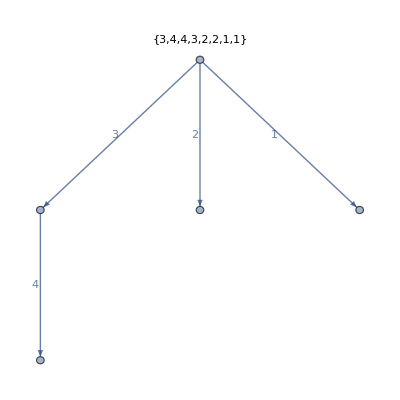
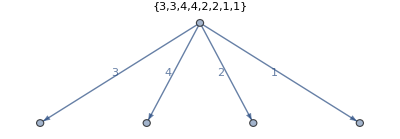
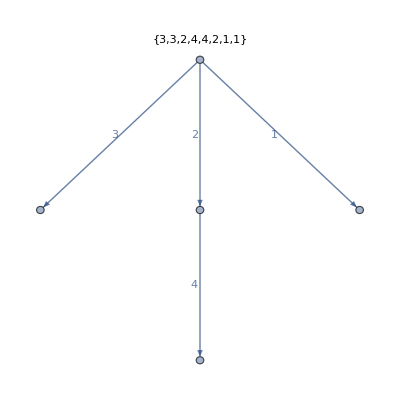
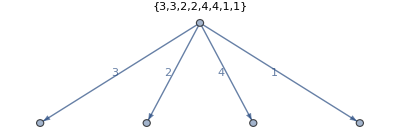
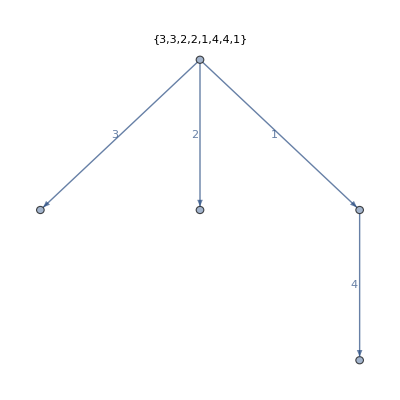
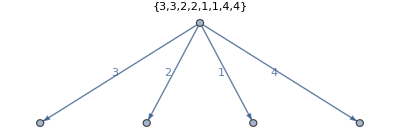
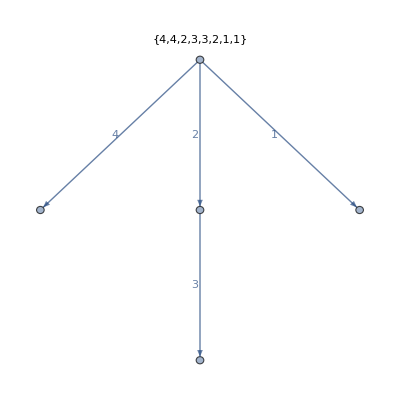
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[StirlingPermutationGraph[#,PlotLabel->#]&/@StirlingPermutations[4],5],Dividers->All]
```

Examples of displaying Stirling permutations:

```mathematica
Multicolumn[Sort@StirlingPermutations@3,5,Appearance->"Horizontal"]
```

{1,1,2,2,3,3} | {1,1,2,3,3,2} | {1,1,3,3,2,2} | {1,2,2,1,3,3} | {1,2,2,3,3,1}
{1,2,3,3,2,1} | {1,3,3,1,2,2} | {1,3,3,2,2,1} | {2,2,1,1,3,3} | {2,2,1,3,3,1}
{2,2,3,3,1,1} | {2,3,3,2,1,1} | {3,3,1,1,2,2} | {3,3,1,2,2,1} | {3,3,2,2,1,1}

```mathematica
Multicolumn[Sort@StirlingPermutations@4,3,Appearance->"Horizontal"]
```

{1,1,2,2,3,3,4,4} | {1,1,2,2,3,4,4,3} | {1,1,2,2,4,4,3,3}
{1,1,2,3,3,2,4,4} | {1,1,2,3,3,4,4,2} | {1,1,2,3,4,4,3,2}
{1,1,2,4,4,2,3,3} | {1,1,2,4,4,3,3,2} | {1,1,3,3,2,2,4,4}
{1,1,3,3,2,4,4,2} | {1,1,3,3,4,4,2,2} | {1,1,3,4,4,3,2,2}
{1,1,4,4,2,2,3,3} | {1,1,4,4,2,3,3,2} | {1,1,4,4,3,3,2,2}
{1,2,2,1,3,3,4,4} | {1,2,2,1,3,4,4,3} | {1,2,2,1,4,4,3,3}
{1,2,2,3,3,1,4,4} | {1,2,2,3,3,4,4,1} | {1,2,2,3,4,4,3,1}
{1,2,2,4,4,1,3,3} | {1,2,2,4,4,3,3,1} | {1,2,3,3,2,1,4,4}
{1,2,3,3,2,4,4,1} | {1,2,3,3,4,4,2,1} | {1,2,3,4,4,3,2,1}
{1,2,4,4,2,1,3,3} | {1,2,4,4,2,3,3,1} | {1,2,4,4,3,3,2,1}
{1,3,3,1,2,2,4,4} | {1,3,3,1,2,4,4,2} | {1,3,3,1,4,4,2,2}
{1,3,3,2,2,1,4,4} | {1,3,3,2,2,4,4,1} | {1,3,3,2,4,4,2,1}
{1,3,3,4,4,1,2,2} | {1,3,3,4,4,2,2,1} | {1,3,4,4,3,1,2,2}
{1,3,4,4,3,2,2,1} | {1,4,4,1,2,2,3,3} | {1,4,4,1,2,3,3,2}
{1,4,4,1,3,3,2,2} | {1,4,4,2,2,1,3,3} | {1,4,4,2,2,3,3,1}
{1,4,4,2,3,3,2,1} | {1,4,4,3,3,1,2,2} | {1,4,4,3,3,2,2,1}
{2,2,1,1,3,3,4,4} | {2,2,1,1,3,4,4,3} | {2,2,1,1,4,4,3,3}
{2,2,1,3,3,1,4,4} | {2,2,1,3,3,4,4,1} | {2,2,1,3,4,4,3,1}
{2,2,1,4,4,1,3,3} | {2,2,1,4,4,3,3,1} | {2,2,3,3,1,1,4,4}
{2,2,3,3,1,4,4,1} | {2,2,3,3,4,4,1,1} | {2,2,3,4,4,3,1,1}
{2,2,4,4,1,1,3,3} | {2,2,4,4,1,3,3,1} | {2,2,4,4,3,3,1,1}
{2,3,3,2,1,1,4,4} | {2,3,3,2,1,4,4,1} | {2,3,3,2,4,4,1,1}
{2,3,3,4,4,2,1,1} | {2,3,4,4,3,2,1,1} | {2,4,4,2,1,1,3,3}
{2,4,4,2,1,3,3,1} | {2,4,4,2,3,3,1,1} | {2,4,4,3,3,2,1,1}
{3,3,1,1,2,2,4,4} | {3,3,1,1,2,4,4,2} | {3,3,1,1,4,4,2,2}
{3,3,1,2,2,1,4,4} | {3,3,1,2,2,4,4,1} | {3,3,1,2,4,4,2,1}
{3,3,1,4,4,1,2,2} | {3,3,1,4,4,2,2,1} | {3,3,2,2,1,1,4,4}
{3,3,2,2,1,4,4,1} | {3,3,2,2,4,4,1,1} | {3,3,2,4,4,2,1,1}
{3,3,4,4,1,1,2,2} | {3,3,4,4,1,2,2,1} | {3,3,4,4,2,2,1,1}
{3,4,4,3,1,1,2,2} | {3,4,4,3,1,2,2,1} | {3,4,4,3,2,2,1,1}
{4,4,1,1,2,2,3,3} | {4,4,1,1,2,3,3,2} | {4,4,1,1,3,3,2,2}
{4,4,1,2,2,1,3,3} | {4,4,1,2,2,3,3,1} | {4,4,1,2,3,3,2,1}
{4,4,1,3,3,1,2,2} | {4,4,1,3,3,2,2,1} | {4,4,2,2,1,1,3,3}
{4,4,2,2,1,3,3,1} | {4,4,2,2,3,3,1,1} | {4,4,2,3,3,2,1,1}
{4,4,3,3,1,1,2,2} | {4,4,3,3,1,2,2,1} | {4,4,3,3,2,2,1,1}

```mathematica
Length[StirlingPermutations@#]&/@Range[9]
```

{1,3,15,105,945,10395,135135,2027025,34459425}

```mathematica
numberofStirlingPermutations[1]=1;
numberofStirlingPermutations[k_]:=(2 k-1) numberofStirlingPermutations[k-1]

numberofStirlingPermutations/@Range[15]
```

{1,3,15,105,945,10395,135135,2027025,34459425,654729075,13749310575,316234143225,7905853580625,213458046676875,6190283353629375}

```mathematica
ClearAll[veAdd,eTrees,postmanTour]

veAdd[g_,opts:OptionsPattern[]]:=Module[{vl=VertexList[g],voc=VertexOutComponent[g,#,1]&/@VertexList[g],vc=VertexCount[g]},Flatten[Function[x,Graph[Insert[vl,vc,1+VertexIndex[g,#]],Append[EdgeList[g],First[x]->vc],GraphLayout->{"LayeredEmbedding","RootVertex"->0},EdgeLabels->{e_:>Placed[Last@e,{Left,"Middle"}]},opts]&/@x]/@voc]]

eTrees[1,opts:OptionsPattern[]]:={Graph[{0,1},{0->1},opts]};

eTrees[k_,opts:OptionsPattern[]]:=Flatten[veAdd[#,opts]&/@eTrees[k-1]]

postmanTour[t_]:=Module[{ug=UndirectedGraph[t,Options[t]/. DirectedEdge->UndirectedEdge]},PropertyValue[{ug,#},EdgeLabels][[1]]&/@Reverse[FindPostmanTour[ug][[1]]]]
```

```mathematica
Multicolumn[Sort[postmanTour/@eTrees[3]],5,Appearance->"Horizontal"]
```

{1,1,2,2,3,3} | {1,1,2,3,3,2} | {1,1,3,3,2,2} | {1,2,2,1,3,3} | {1,2,2,3,3,1}
{1,2,3,3,2,1} | {1,3,3,1,2,2} | {1,3,3,2,2,1} | {2,2,1,1,3,3} | {2,2,1,3,3,1}
{2,2,3,3,1,1} | {2,3,3,2,1,1} | {3,3,1,1,2,2} | {3,3,1,2,2,1} | {3,3,2,2,1,1}

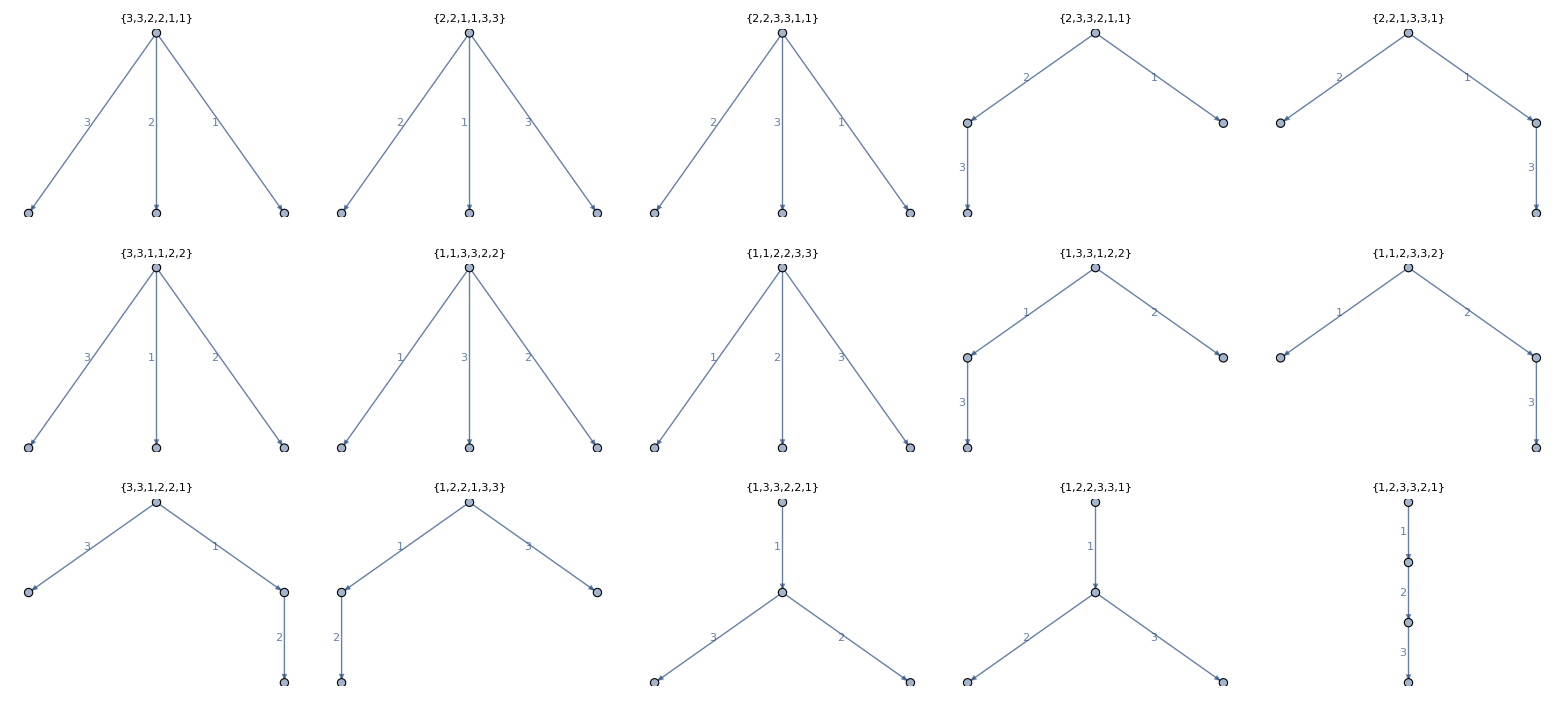

```mathematica
Grid[Partition[Show[#,PlotLabel->postmanTour@#]&/@eTrees[3,VertexShapeFunction->(Disk[#,Offset[3]]&),AspectRatio->1],5],Dividers->All]
```

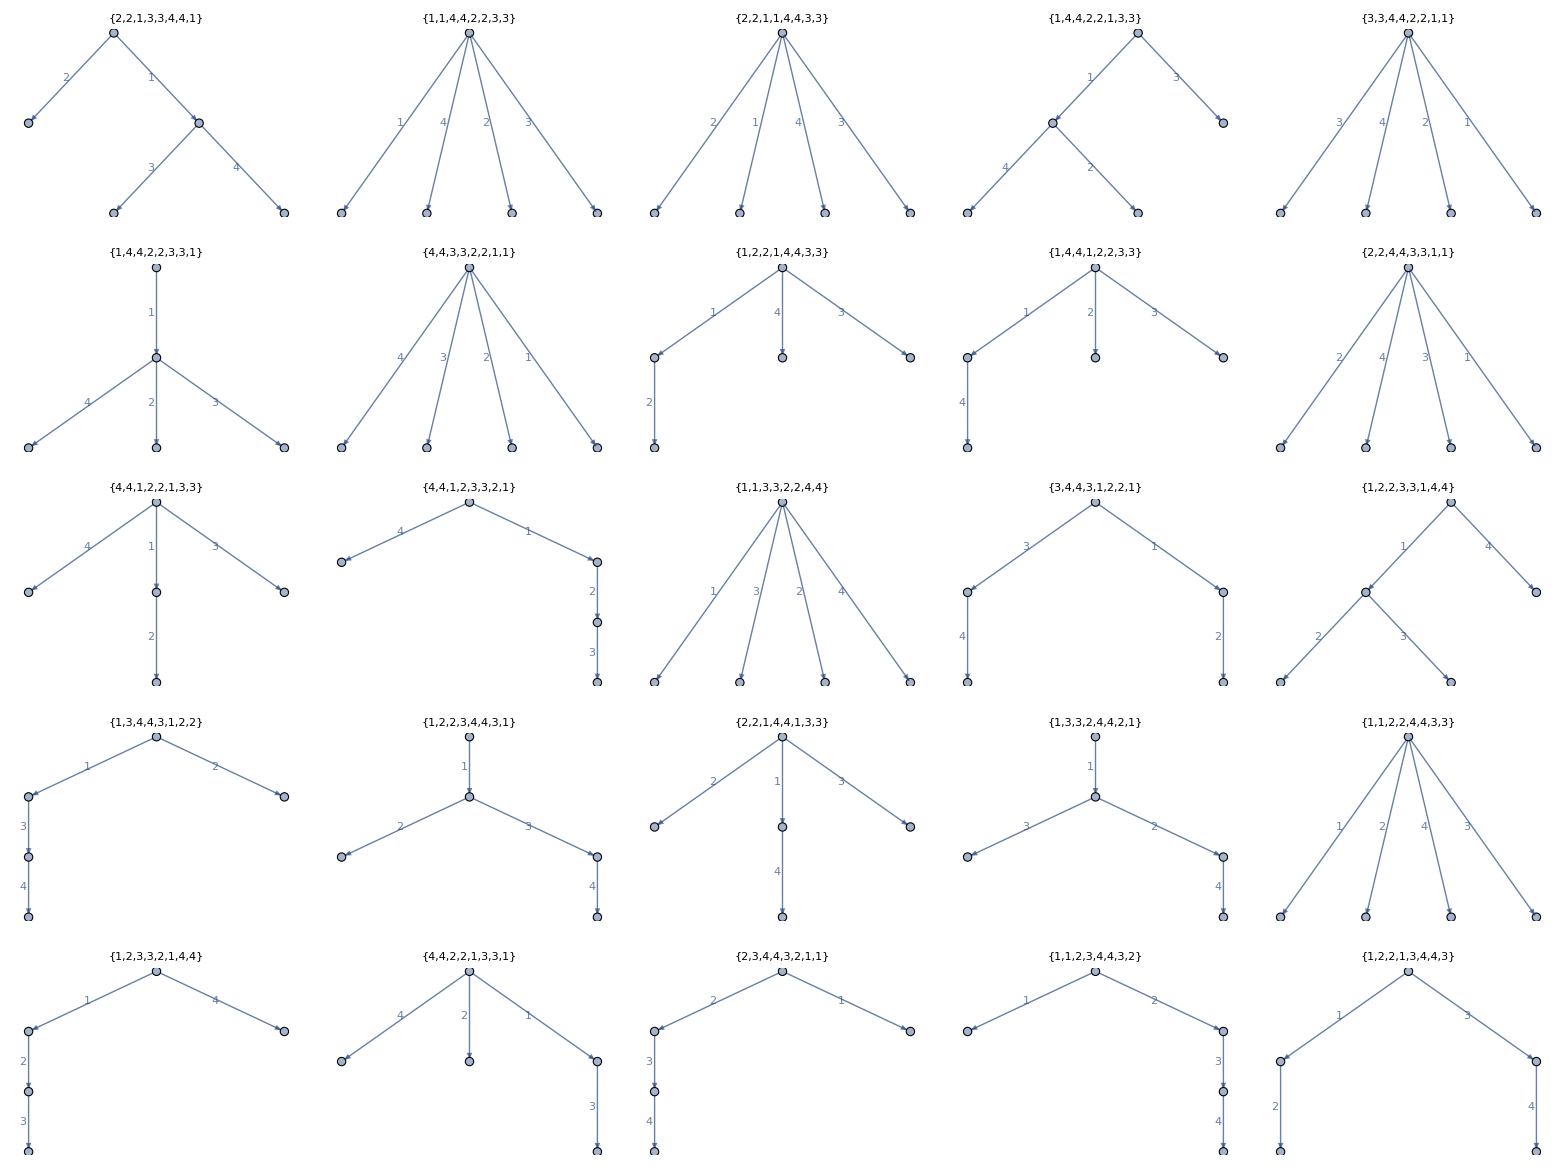

```mathematica
Grid[Partition[Show[#,PlotLabel->postmanTour@#]&/@RandomSample[eTrees[4,VertexShapeFunction->(Disk[#,Offset[3]]&),AspectRatio->1,ImageSize->150],25],5],Dividers->All]
```

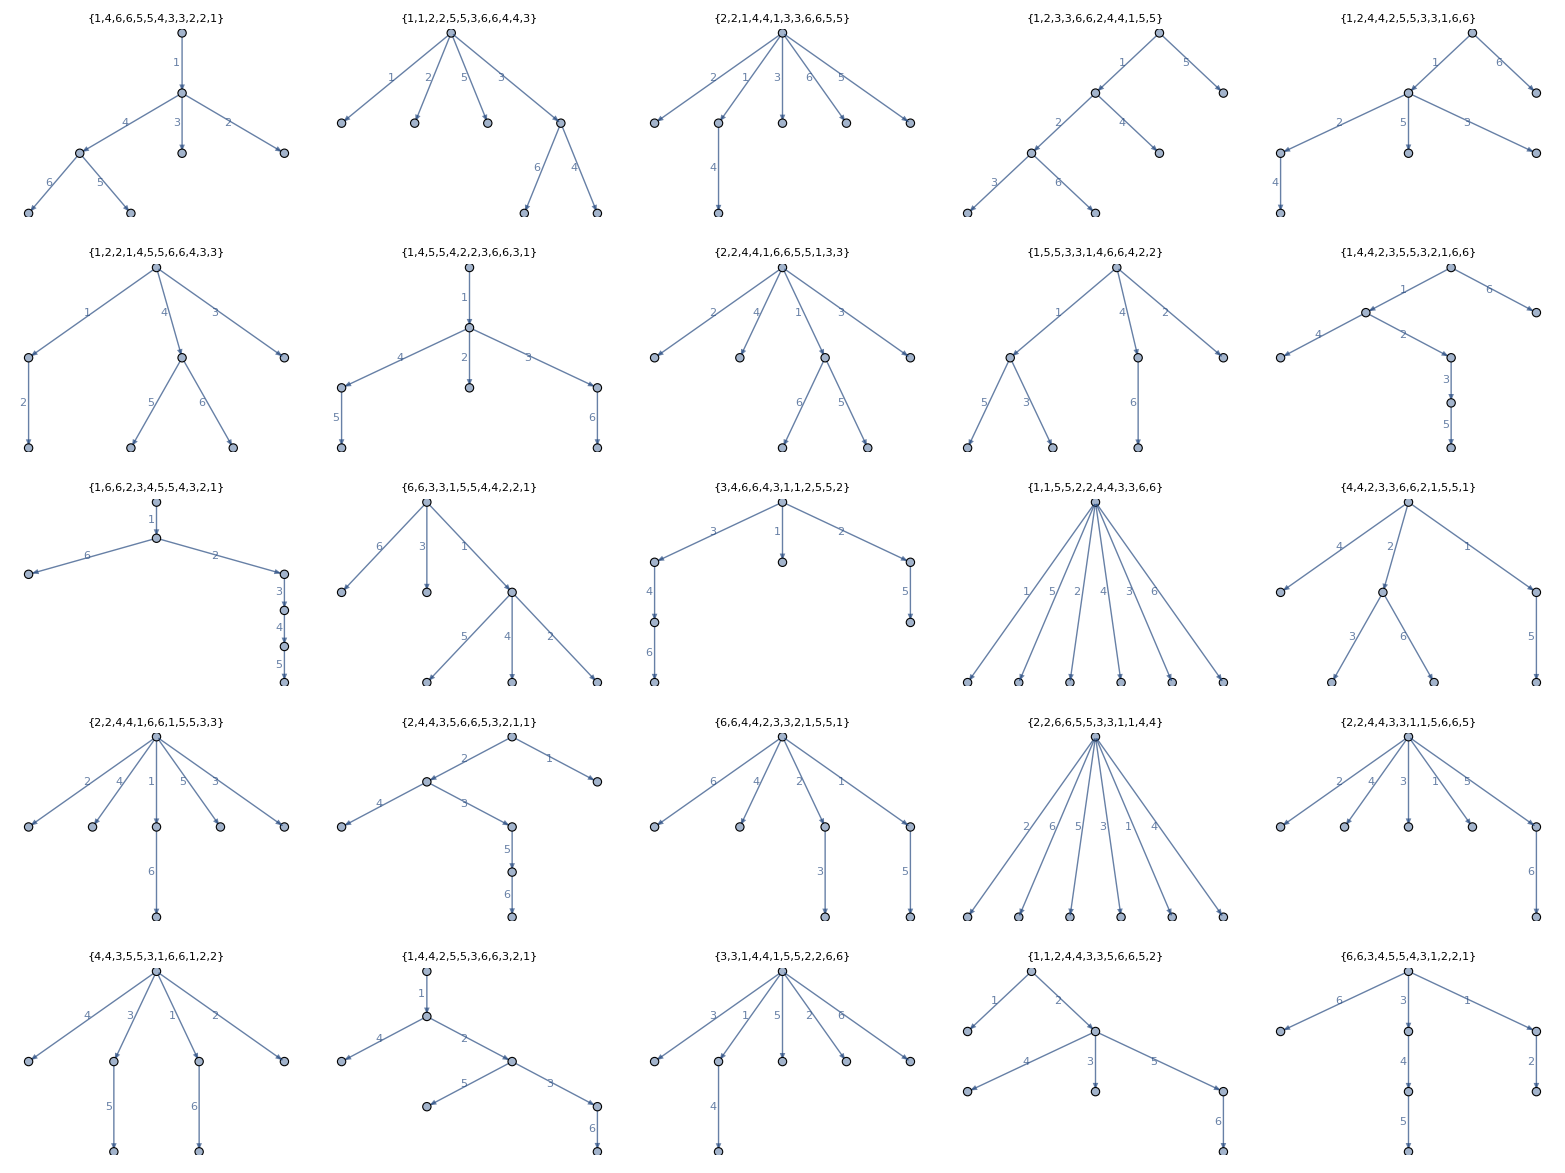

```mathematica
Grid[Partition[Show[#,PlotLabel->postmanTour@#]&/@RandomSample[eTrees[6,VertexShapeFunction->(Disk[#,Offset[3]]&),AspectRatio->1,ImageSize->170],25],5],Dividers->All]
```

This uses Knuth's algorithm L.

```mathematica
stirlingPermutations[n_Integer?Positive]:=Module[{p=Quotient[Range[2 n-1],2,-1],j,k},Reap[While[True,If[!MatchQ[p,{___,a_,b__,a_,___}/;Min[{b}]<a],Sow[ReplaceAll[p,n->Sequence[n,n]]]];
j=2 (n-1);
While[j>0&&p[[j]]>=p[[j+1]],j--];
If[j==0,Break[]];
k=2 n-1;
While[p[[j]]>=p[[k]],k--];
p[[{j,k}]]=p[[{k,j}]];
p[[j+1;;]]=p[[-1;;j+1;;-1]]]][[-1,1]]]
```

```mathematica
stirlingPermutations[3]
```

{{1,1,2,2,3,3},{1,1,2,3,3,2},{1,1,3,3,2,2},{1,2,2,1,3,3},{1,2,2,3,3,1},{1,2,3,3,2,1},{1,3,3,1,2,2},{1,3,3,2,2,1},{2,2,1,1,3,3},{2,2,1,3,3,1},{2,2,3,3,1,1},{2,3,3,2,1,1},{3,3,1,1,2,2},{3,3,1,2,2,1},{3,3,2,2,1,1}}

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/tutorial/Stirlingpermutation

### Keywords